## Examples Using The Chemical Space Function

### D5 Receptor Activities - Simple Graph generation

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/src/nb

```mathematica
csvData=Import["../../Data/D5Activities.csv"];
```

```mathematica
csvData[[;;1]]
```

{{Molecule ChEMBL ID";"Molecule Name";"Molecule Max Phase";"Molecular Weight";"#RO5 Violations";"AlogP";"Compound Key";"Smiles";"Standard Type";"Standard Relation";"Standard Value";"Standard Units";"pChEMBL Value";"Data Validity Comment";"Comment";"Uo Units";"Ligand Efficiency BEI";"Ligand Efficiency LE";"Ligand Efficiency LLE";"Ligand Efficiency SEI";"Potential Duplicate";"Assay ChEMBL ID";"Assay Description";"Assay Type";"BAO Format ID";"BAO Label";"Assay Organism";"Assay Tissue ChEMBL ID";"Assay Tissue Name";"Assay Cell Type";"Assay Subcellular Fraction";"Assay Parameters";"Assay Variant Accession";"Assay Variant Mutation";"Target ChEMBL ID";"Target Name";"Target Organism";"Target Type";"Document ChEMBL ID";"Source ID";"Source Description";"Document Journal";"Document Year";"Cell ChEMBL ID";"Properties";"Action Type}}

```mathematica
<<../ChemicalSpaceFunction.wl
```

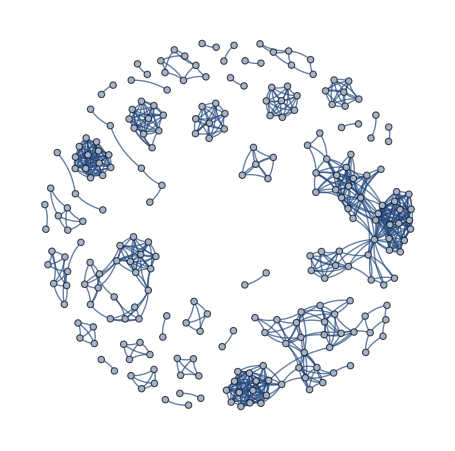

```mathematica
graph=chemicalSpaceNetwork["../../Data/D5Activities.csv",0.4]
```

### Embedding Molecules

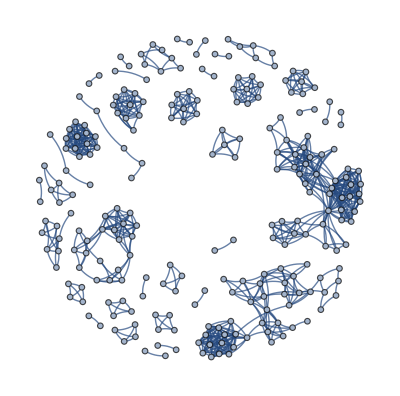

```mathematica
graphWithMolecules=chemicalSpaceNetwork["../../Data/D5Activities.csv",0.4,"Embed Molecules"->True]
```